# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[2k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev3DoppTestscSinlge[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Figure

## Module

Module for the figure

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 80/1000,
Select[Range[-0.01,0.01,0.00016],#≥ 0.002∨#≤ -0.002&]*10^9,
Range[-0.007,0.007,0.00016]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev4DoppTestscγ[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Select[
Flatten[{Range[-0.007,0.001,0.00016],Range[-0.001,0.001,0.000016],Range[-0.001,0.007,0.00016]}]
,#≥ 0.0005∨#≤ -0.0005&]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.007,0.007,0.00016]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 100/1000,
Select[Range[-0.20,0.05,0.000083],#≥ 0.0015∨#≤ -0.0015&]*10^9,
Range[-0.17,0.08,0.000083]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.05,0.08,0.000033]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc2[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.005,0.0015,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc2[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.005,0.0015,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc3[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.05,0.004,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc3[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.05,0.004,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.015,0.007,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.015,0.007,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

## Transmission vs Power

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[65/1000,1/1000]/(2Pi)/(5.750056 10^6)
Ome[142.75/1000,1/1000]/(2Pi)/(5.750056 10^6)
```

10.122

15.0002

γ=0

```mathematica
γ=0;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,100,10}]
]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

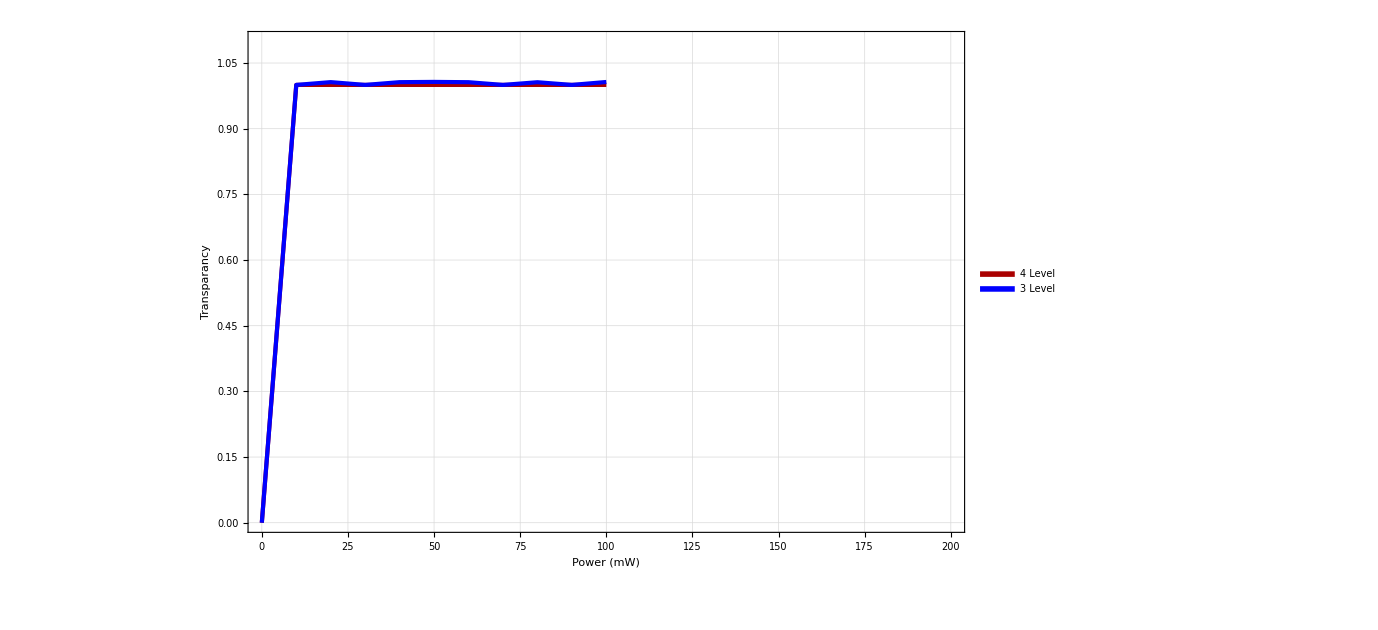

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.1}}]
```

γ=0.1

```mathematica
γ=0.1*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,200,10}]
]
```

General::munfl: Exp[-713.172-383.04 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-730.088-361.543 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-746.068-339.005 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

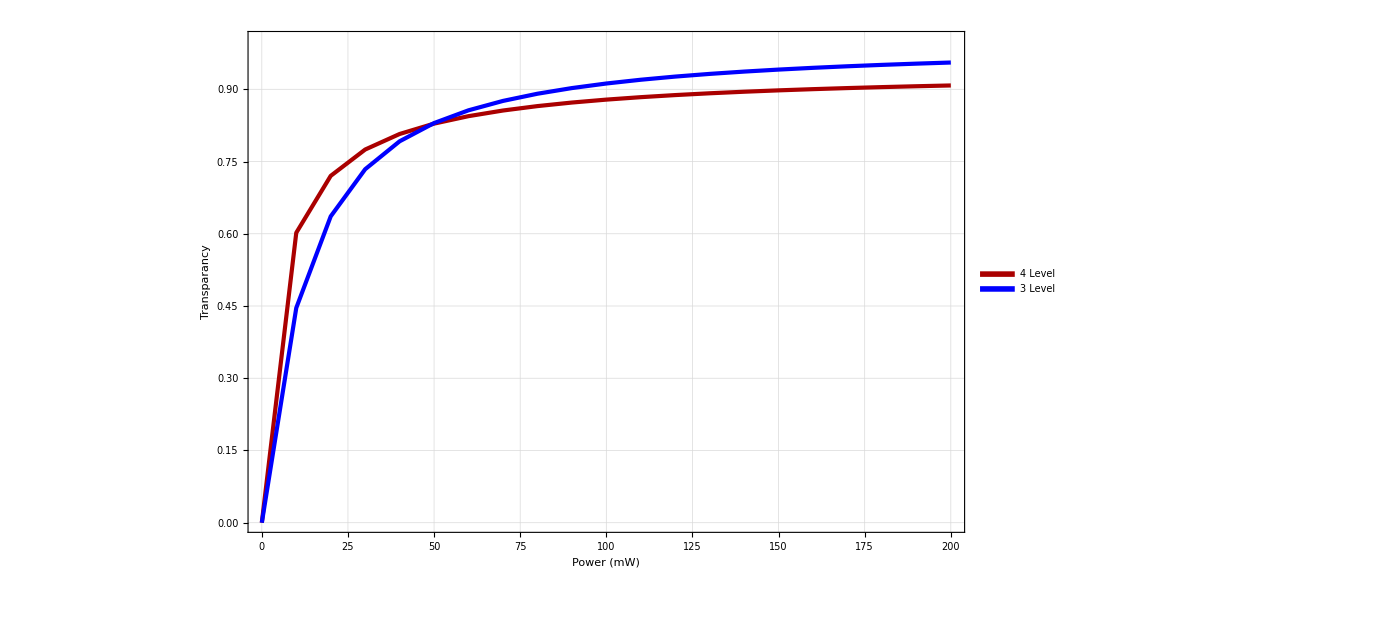

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.0}}]
```

γ=0.25

90

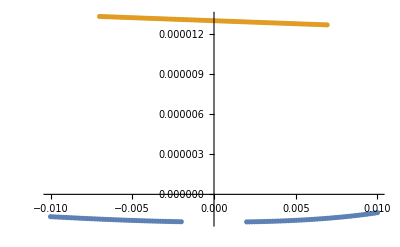

2.02614×10^-6

-2.06189×10^-6

0.0000131636

0.0000129457

{-0.007,-0.00674,-0.00648,-0.00622,-0.00596,-0.0057,-0.00544,-0.00518,-0.00492,-0.00466,-0.0044,-0.00414,-0.00388,-0.00362,-0.00336,-0.0031,-0.00284,-0.00258,-0.00232,-0.00206,-0.0018,-0.00154,-0.00128,-0.00102,0.00106,0.00132,0.00158,0.00184,0.0021,0.00236,0.00262,0.00288,0.00314,0.0034,0.00366,0.00392,0.00418,0.00444,0.0047,0.00496,0.00522,0.00548,0.00574,0.006,0.00626,0.00652,0.00678}

```mathematica
p=90
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list3,list4}]
EIT=Min[DeleteCases[list[[All,2]],Indeterminate]]
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]]

ABS=list1[[Position[list,EIT][[1,1]]]][[2]]
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]]
```

```mathematica
γ=0.25*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,200,2}]
]
```

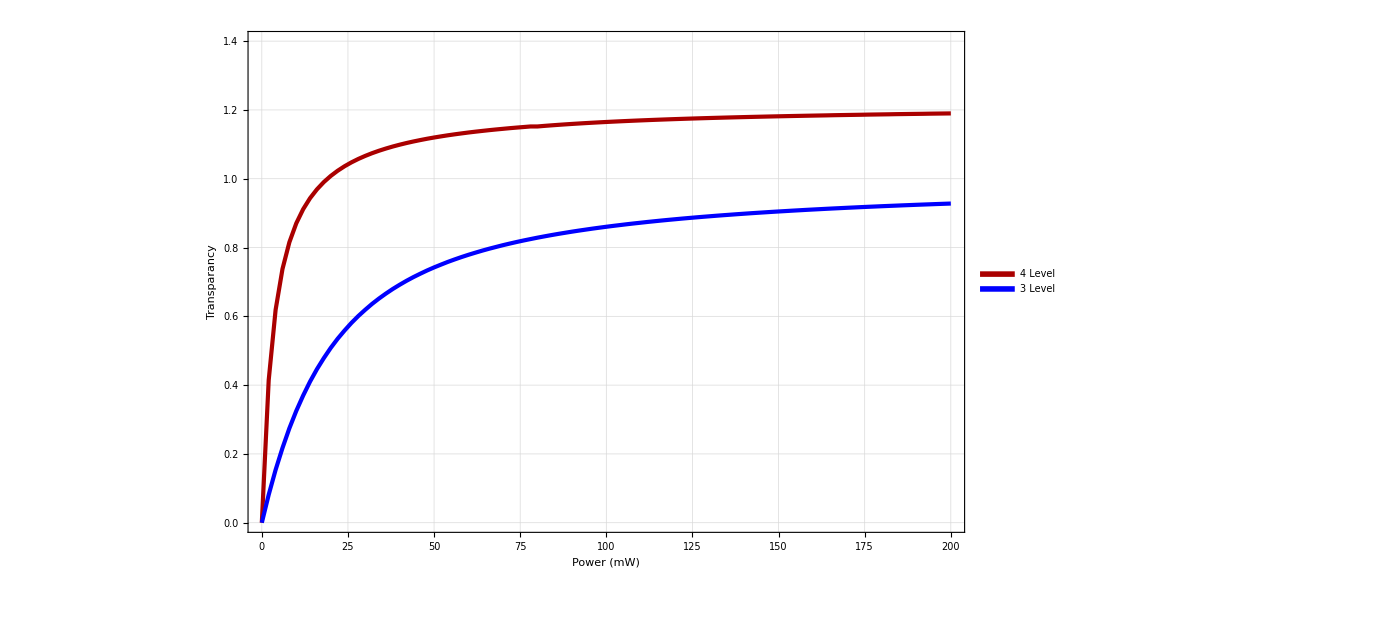

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
tp1=ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.4}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure41.eps",tp1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure41.eps

γ=0.5

```mathematica
γ=0.5*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,100,10}]
]
```

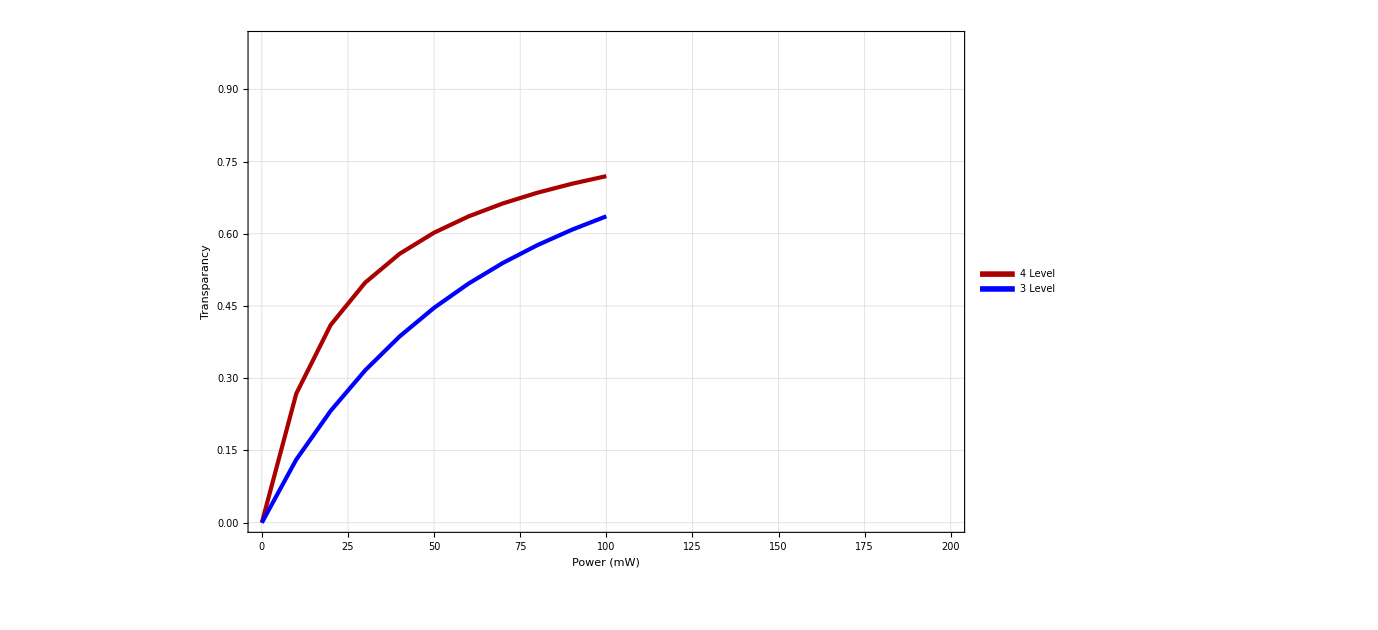

```mathematica
γ=0.5*5.750056;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.0}}]
```

## Trans vs decoherence

P=0γ

```mathematica
p=0;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

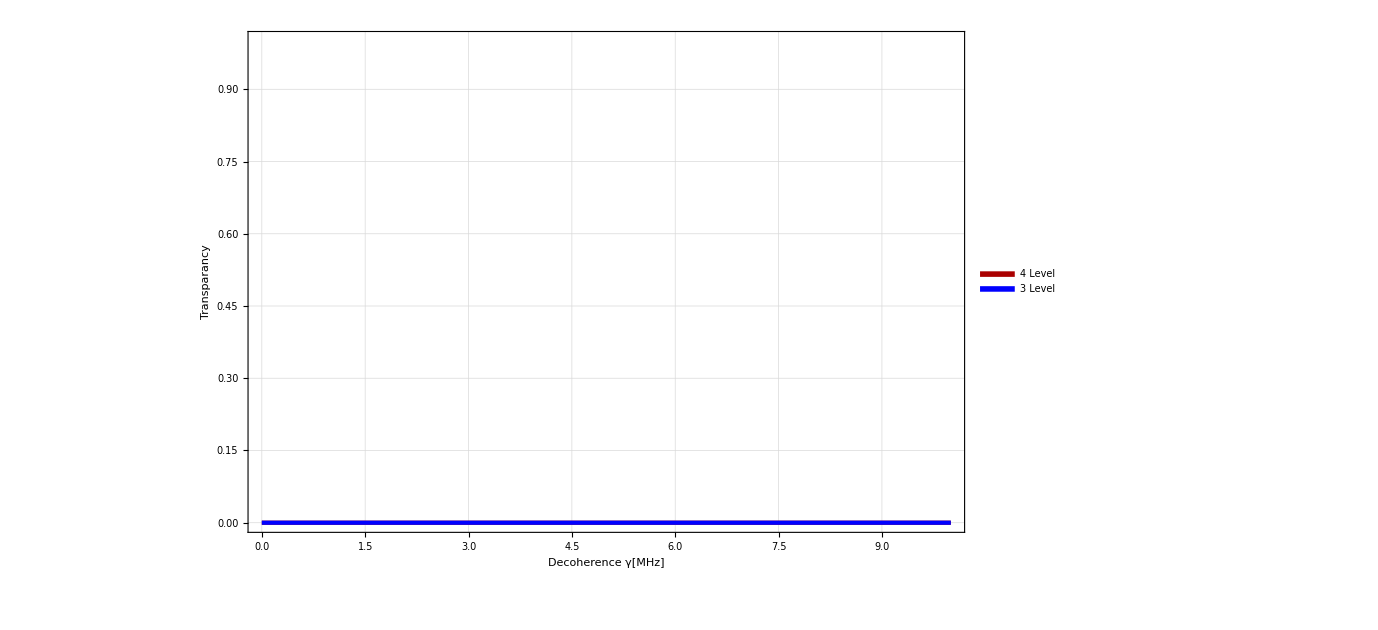

```mathematica
p=0;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

P=2.5γ

```mathematica
p=3.99;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

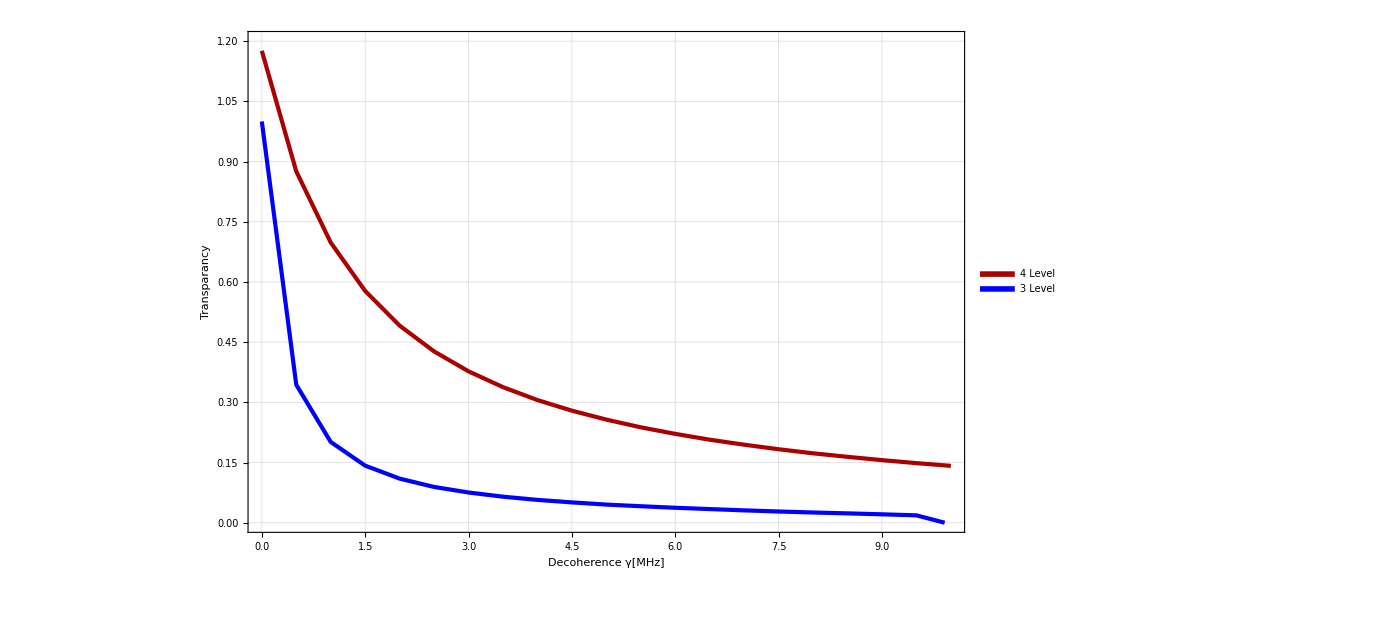

```mathematica
p=3.99;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.2}}]
```

P=5γ

```mathematica
p=15.8;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestscγ[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestscγ[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,3,0.01}]
]
```

```mathematica
nf1=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Tvγ4[p]
nf2=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Tvγ3[p]
```

{{0.,1.21677},{0.00173911,1.21435},{0.00347823,1.21195},{0.00521734,1.20957},{0.00695645,1.20719},{0.00869557,1.20483},{0.0104347,1.2025},{0.0121738,1.20017},{0.0139129,1.19785},{0.015652,1.19552},{0.0173911,1.1932},{0.0191302,1.19089},{0.0208694,1.18857},{0.0226085,1.18626},{0.0243476,1.18395},{0.0260867,1.18165},{0.0278258,1.17934},{0.0295649,1.17704},{0.031304,1.17475},{0.0330432,1.17245},{0.0347823,1.17016},{0.0365214,1.16788},{0.0382605,1.16559},{0.0399996,1.16331},{0.0417387,1.16103},{0.0434778,1.15876},{0.045217,1.15649},{0.0469561,1.15422},{0.0486952,1.15195},{0.0504343,1.14969},{0.0521734,1.14743},{0.0539125,1.14518},{0.0556516,1.14285},{0.0573907,1.14105},{0.0591299,1.13925},{0.060869,1.13745},{0.0626081,1.13566},{0.0643472,1.13386},{0.0660863,1.13207},{0.0678254,1.13028},{0.0695645,1.12849},{0.0713037,1.12671},{0.0730428,1.12492},{0.0747819,1.12314},{0.076521,1.12136},{0.0782601,1.11958},{0.0799992,1.1178},{0.0817383,1.11603},{0.0834774,1.11426},{0.0852166,1.11249},{0.0869557,1.11072},{0.0886948,1.10895},{0.0904339,1.10719},{0.092173,1.10543},{0.0939121,1.10367},{0.0956512,1.10191},{0.0973904,1.10015},{0.0991295,1.0984},{0.100869,1.09665},{0.102608,1.0949},{0.104347,1.09315},{0.106086,1.0914},{0.107825,1.08966},{0.109564,1.08792},{0.111303,1.08618},{0.113042,1.08444},{0.114781,1.08271},{0.116521,1.08099},{0.11826,1.07928},{0.119999,1.07757},{0.121738,1.07587},{0.123477,1.07417},{0.125216,1.07249},{0.126955,1.07081},{0.128694,1.06914},{0.130434,1.06747},{0.132173,1.06581},{0.133912,1.06416},{0.135651,1.06252},{0.13739,1.06088},{0.139129,1.05925},{0.140868,1.05762},{0.142607,1.056},{0.144346,1.05439},{0.146086,1.05279},{0.147825,1.05119},{0.149564,1.04959},{0.151303,1.04801},{0.153042,1.04643},{0.154781,1.04485},{0.15652,1.04328},{0.158259,1.04172},{0.159998,1.04017},{0.161738,1.03861},{0.163477,1.03707},{0.165216,1.03553},{0.166955,1.034},{0.168694,1.03247},{0.170433,1.03095},{0.172172,1.02943},{0.173911,1.02791},{0.17565,1.02641},{0.17739,1.02492},{0.179129,1.02343},{0.180868,1.02194},{0.182607,1.02045},{0.184346,1.01897},{0.186085,1.01748},{0.187824,1.016},{0.189563,1.01453},{0.191302,1.01309},{0.193042,1.01165},{0.194781,1.01022},{0.19652,1.00878},{0.198259,1.00735},{0.199998,1.00592},{0.201737,1.00449},{0.203476,1.00307},{0.205215,1.00164},{0.206955,1.00022},{0.208694,0.998798},{0.210433,0.997403},{0.212172,0.996022},{0.213911,0.994642},{0.21565,0.993264},{0.217389,0.991887},{0.219128,0.990512},{0.220867,0.989139},{0.222607,0.987767},{0.224346,0.986397},{0.226085,0.985029},{0.227824,0.983662},{0.229563,0.982297},{0.231302,0.980964},{0.233041,0.979636},{0.23478,0.978309},{0.236519,0.976984},{0.238259,0.975661},{0.239998,0.974339},{0.241737,0.973019},{0.243476,0.9717},{0.245215,0.970383},{0.246954,0.969067},{0.248693,0.967753},{0.250432,0.966441},{0.252171,0.965155},{0.253911,0.963877},{0.25565,0.962601},{0.257389,0.961326},{0.259128,0.960052},{0.260867,0.95878},{0.262606,0.95751},{0.264345,0.956241},{0.266084,0.954973},{0.267823,0.953707},{0.269563,0.952442},{0.271302,0.951179},{0.273041,0.949917},{0.27478,0.948698},{0.276519,0.947469},{0.278258,0.946241},{0.279997,0.945014},{0.281736,0.943789},{0.283476,0.942565},{0.285215,0.941342},{0.286954,0.940121},{0.288693,0.938902},{0.290432,0.937684},{0.292171,0.936467},{0.29391,0.935251},{0.295649,0.934037},{0.297388,0.932869},{0.299128,0.931685},{0.300867,0.930503},{0.302606,0.929322},{0.304345,0.928142},{0.306084,0.926963},{0.307823,0.925786},{0.309562,0.92461},{0.311301,0.923436},{0.31304,0.922262},{0.31478,0.92109},{0.316519,0.91992},{0.318258,0.918751},{0.319997,0.917583},{0.321736,0.91648},{0.323475,0.915341},{0.325214,0.914202},{0.326953,0.913065},{0.328692,0.911929},{0.330432,0.910794},{0.332171,0.909661},{0.33391,0.908529},{0.335649,0.907398},{0.337388,0.906269},{0.339127,0.90514},{0.340866,0.904014},{0.342605,0.902888},{0.344344,0.901764},{0.346084,0.900712},{0.347823,0.899614},{0.349562,0.898517},{0.351301,0.897421},{0.35304,0.896327},{0.354779,0.895233},{0.356518,0.894141},{0.358257,0.893051},{0.359996,0.891961},{0.361736,0.890873},{0.363475,0.889786},{0.365214,0.8887},{0.366953,0.887615},{0.368692,0.886532},{0.370431,0.885519},{0.37217,0.88446},{0.373909,0.883402},{0.375649,0.882346},{0.377388,0.881291},{0.379127,0.880236},{0.380866,0.879183},{0.382605,0.878132},{0.384344,0.877081},{0.386083,0.876032},{0.387822,0.874983},{0.389561,0.873936},{0.391301,0.872891},{0.39304,0.871846},{0.394779,0.870803},{0.396518,0.869839},{0.398257,0.868819},{0.399996,0.8678},{0.401735,0.866781},{0.403474,0.865764},{0.405213,0.864748},{0.406953,0.863733},{0.408692,0.86272},{0.410431,0.861707},{0.41217,0.860696},{0.413909,0.859685},{0.415648,0.858676},{0.417387,0.857668},{0.419126,0.856661},{0.420865,0.855655},{0.422605,0.854651},{0.424344,0.853747},{0.426083,0.852764},{0.427822,0.851782},{0.429561,0.850801},{0.4313,0.849821},{0.433039,0.848842},{0.434778,0.847864},{0.436517,0.846888},{0.438257,0.845912},{0.439996,0.844938},{0.441735,0.843964},{0.443474,0.842992},{0.445213,0.842021},{0.446952,0.841051},{0.448691,0.840082},{0.45043,0.839206},{0.45217,0.838257},{0.453909,0.83731},{0.455648,0.836363},{0.457387,0.835417},{0.459126,0.834473},{0.460865,0.833529},{0.462604,0.832587},{0.464343,0.831645},{0.466082,0.830705},{0.467822,0.829766},{0.469561,0.828827},{0.4713,0.82789},{0.473039,0.826954},{0.474778,0.826019},{0.476517,0.825085},{0.478256,0.824152},{0.479995,0.823332},{0.481734,0.822418},{0.483474,0.821505},{0.485213,0.820593},{0.486952,0.819682},{0.488691,0.818772},{0.49043,0.817863},{0.492169,0.816954},{0.493908,0.816047},{0.495647,0.815141},{0.497386,0.814236},{0.499126,0.813332},{0.500865,0.812429},{0.502604,0.811528},{0.504343,0.810627},{0.506082,0.809727},{0.507821,0.808935},{0.50956,0.808053},{0.511299,0.807172},{0.513038,0.806292},{0.514778,0.805413},{0.516517,0.804535},{0.518256,0.803657},{0.519995,0.802781},{0.521734,0.801906}}

{{0.,1.},{0.00173911,1.},{0.00347823,0.986142},{0.00521734,0.979633},{0.00695645,0.97313},{0.00869557,0.966634},{0.0104347,0.960286},{0.0121738,0.954055},{0.0139129,0.94785},{0.015652,0.941671},{0.0173911,0.935518},{0.0191302,0.929391},{0.0208694,0.923293},{0.0226085,0.917223},{0.0243476,0.911181},{0.0260867,0.905168},{0.0278258,0.899184},{0.0295649,0.89323},{0.031304,0.887307},{0.0330432,0.881414},{0.0347823,0.875551},{0.0365214,0.86972},{0.0382605,0.86392},{0.0399996,0.858152},{0.0417387,0.852416},{0.0434778,0.846712},{0.045217,0.84104},{0.0469561,0.835401},{0.0486952,0.829795},{0.0504343,0.824222},{0.0521734,0.818683},{0.0539125,0.813176},{0.0556516,0.807704},{0.0573907,0.802655},{0.0591299,0.797575},{0.060869,0.792528},{0.0626081,0.787516},{0.0643472,0.782537},{0.0660863,0.777592},{0.0678254,0.77268},{0.0695645,0.767801},{0.0713037,0.762955},{0.0730428,0.758143},{0.0747819,0.753363},{0.076521,0.748615},{0.0782601,0.7439},{0.0799992,0.739217},{0.0817383,0.734567},{0.0834774,0.729948},{0.0852166,0.725362},{0.0869557,0.720807},{0.0886948,0.716284},{0.0904339,0.711792},{0.092173,0.707332},{0.0939121,0.702903},{0.0956512,0.698506},{0.0973904,0.694139},{0.0991295,0.689803},{0.100869,0.685498},{0.102608,0.681586},{0.104347,0.677631},{0.106086,0.673703},{0.107825,0.669802},{0.109564,0.665926},{0.111303,0.662077},{0.113042,0.658253},{0.114781,0.654456},{0.116521,0.650684},{0.11826,0.646937},{0.119999,0.643216},{0.121738,0.63952},{0.123477,0.63585},{0.125216,0.632204},{0.126955,0.628583},{0.128694,0.624987},{0.130434,0.621416},{0.132173,0.617869},{0.133912,0.614347},{0.135651,0.610848},{0.13739,0.607374},{0.139129,0.603924},{0.140868,0.600498},{0.142607,0.597095},{0.144346,0.593716},{0.146086,0.590762},{0.147825,0.587654},{0.149564,0.584566},{0.151303,0.581498},{0.153042,0.578449},{0.154781,0.575419},{0.15652,0.572408},{0.158259,0.569416},{0.159998,0.566444},{0.161738,0.56349},{0.163477,0.560556},{0.165216,0.55764},{0.166955,0.554742},{0.168694,0.551864},{0.170433,0.549003},{0.172172,0.546161},{0.173911,0.543338},{0.17565,0.540532},{0.17739,0.537745},{0.179129,0.534976},{0.180868,0.532224},{0.182607,0.52949},{0.184346,0.526775},{0.186085,0.524076},{0.187824,0.521745},{0.189563,0.519253},{0.191302,0.516775},{0.193042,0.514311},{0.194781,0.511862},{0.19652,0.509427},{0.198259,0.507006},{0.199998,0.5046},{0.201737,0.502208},{0.203476,0.49983},{0.205215,0.497466},{0.206955,0.495116},{0.208694,0.49278},{0.210433,0.490458},{0.212172,0.48815},{0.213911,0.485855},{0.21565,0.483574},{0.217389,0.481307},{0.219128,0.479053},{0.220867,0.476813},{0.222607,0.474586},{0.224346,0.472372},{0.226085,0.470172},{0.227824,0.467985},{0.229563,0.466167},{0.231302,0.464135},{0.233041,0.462115},{0.23478,0.460105},{0.236519,0.458106},{0.238259,0.456118},{0.239998,0.454141},{0.241737,0.452175},{0.243476,0.450219},{0.245215,0.448274},{0.246954,0.44634},{0.248693,0.444416},{0.250432,0.442503},{0.252171,0.4406},{0.253911,0.438708},{0.25565,0.436826},{0.257389,0.434955},{0.259128,0.433094},{0.260867,0.431243},{0.262606,0.429402},{0.264345,0.427572},{0.266084,0.425751},{0.267823,0.423941},{0.269563,0.422141},{0.271302,0.420721},{0.273041,0.419039},{0.27478,0.417366},{0.276519,0.415702},{0.278258,0.414045},{0.279997,0.412397},{0.281736,0.410758},{0.283476,0.409127},{0.285215,0.407503},{0.286954,0.405889},{0.288693,0.404282},{0.290432,0.402683},{0.292171,0.401093},{0.29391,0.399511},{0.295649,0.397936},{0.297388,0.39637},{0.299128,0.394812},{0.300867,0.393261},{0.302606,0.391719},{0.304345,0.390184},{0.306084,0.388658},{0.307823,0.387139},{0.309562,0.385628},{0.311301,0.384124},{0.31304,0.383006},{0.31478,0.381595},{0.316519,0.380191},{0.318258,0.378792},{0.319997,0.377401},{0.321736,0.376016},{0.323475,0.374637},{0.325214,0.373265},{0.326953,0.371899},{0.328692,0.37054},{0.330432,0.369187},{0.332171,0.367841},{0.33391,0.366501},{0.335649,0.365167},{0.337388,0.363839},{0.339127,0.362518},{0.340866,0.361203},{0.342605,0.359894},{0.344344,0.358592},{0.346084,0.357296},{0.347823,0.356005},{0.349562,0.354721},{0.351301,0.353444},{0.35304,0.352172},{0.354779,0.351283},{0.356518,0.350083},{0.358257,0.348889},{0.359996,0.3477},{0.361736,0.346516},{0.363475,0.345338},{0.365214,0.344164},{0.366953,0.342996},{0.368692,0.341833},{0.370431,0.340675},{0.37217,0.339521},{0.373909,0.338374},{0.375649,0.337231},{0.377388,0.336093},{0.379127,0.33496},{0.380866,0.333832},{0.382605,0.332709},{0.384344,0.331591},{0.386083,0.330478},{0.387822,0.32937},{0.389561,0.328267},{0.391301,0.327169},{0.39304,0.326075},{0.394779,0.324987},{0.396518,0.323903},{0.398257,0.323242},{0.399996,0.322215},{0.401735,0.321193},{0.403474,0.320175},{0.405213,0.31916},{0.406953,0.318151},{0.408692,0.317145},{0.410431,0.316143},{0.41217,0.315146},{0.413909,0.314152},{0.415648,0.313163},{0.417387,0.312178},{0.419126,0.311196},{0.420865,0.310219},{0.422605,0.309246},{0.424344,0.308277},{0.426083,0.307312},{0.427822,0.306351},{0.429561,0.305394},{0.4313,0.304441},{0.433039,0.303491},{0.434778,0.302546},{0.436517,0.301605},{0.438257,0.300667},{0.439996,0.30013},{0.441735,0.299239},{0.443474,0.298351},{0.445213,0.297467},{0.446952,0.296586},{0.448691,0.295709},{0.45043,0.294834},{0.45217,0.293963},{0.453909,0.293096},{0.455648,0.292232},{0.457387,0.291371},{0.459126,0.290514},{0.460865,0.289659},{0.462604,0.288809},{0.464343,0.287961},{0.466082,0.287117},{0.467822,0.286276},{0.469561,0.285438},{0.4713,0.284604},{0.473039,0.283773},{0.474778,0.282945},{0.476517,0.28212},{0.478256,0.281298},{0.479995,0.28048},{0.481734,0.279665},{0.483474,0.279259},{0.485213,0.278482},{0.486952,0.277707},{0.488691,0.276935},{0.49043,0.276166},{0.492169,0.275399},{0.493908,0.274635},{0.495647,0.273875},{0.497386,0.273116},{0.499126,0.272361},{0.500865,0.271609},{0.502604,0.270859},{0.504343,0.270112},{0.506082,0.269367},{0.507821,0.268626},{0.50956,0.267887},{0.511299,0.26715},{0.513038,0.266417},{0.514778,0.265686},{0.516517,0.264958},{0.518256,0.264232},{0.519995,0.26351},{0.521734,0.262789}}

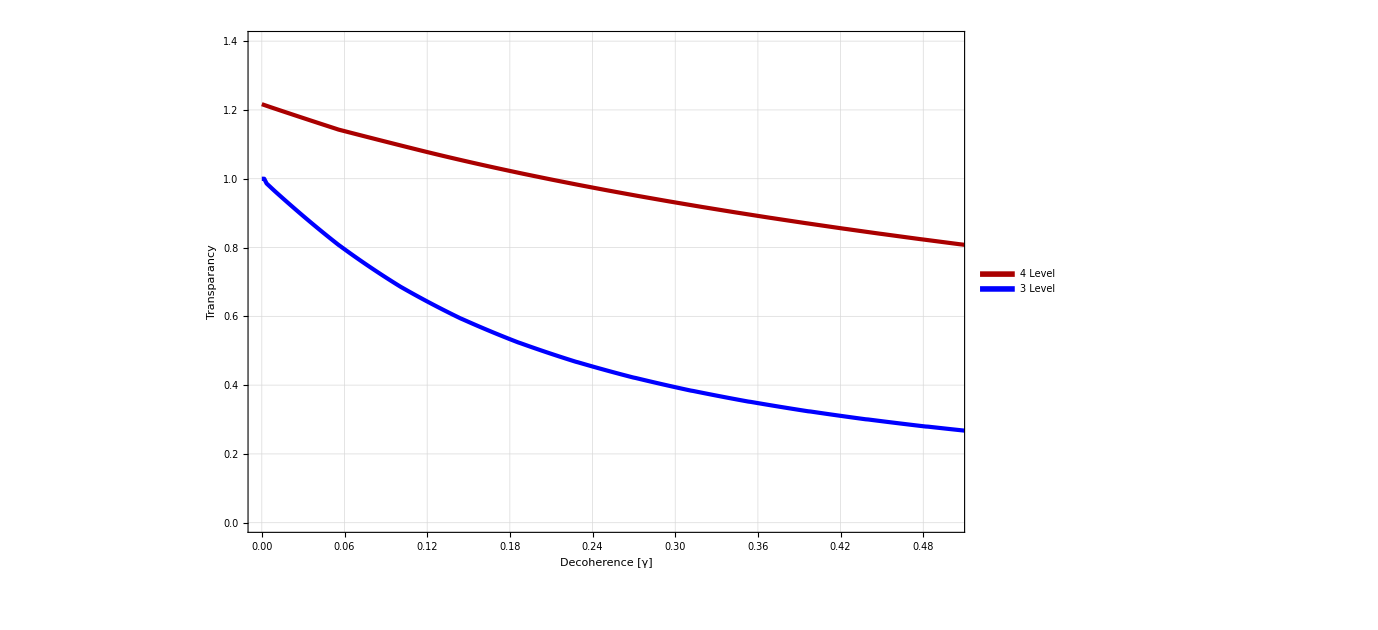

```mathematica
p=15.8;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
td1=ListPlot[{nf1,nf2},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence [γ]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,0.5},{0.0,1.4}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure42.eps",td1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure42.eps

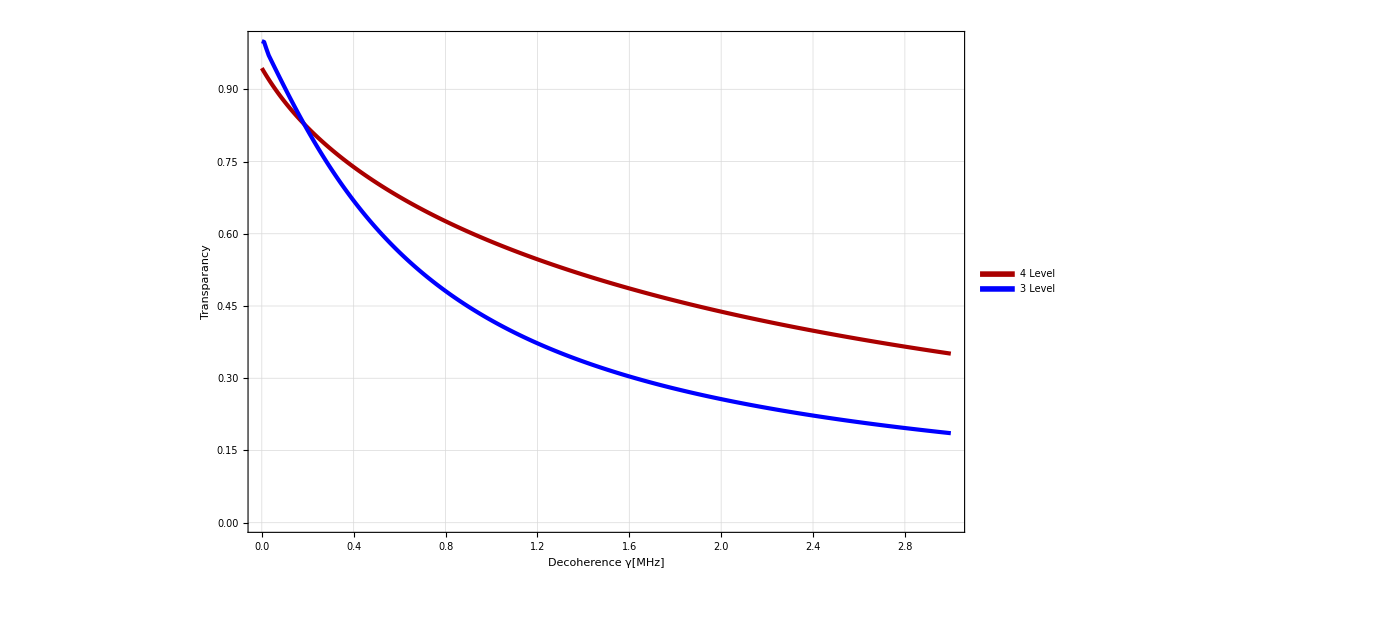

```mathematica
p=15.8;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
td1=ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,3},{0,1.0}}]
```

P=10γ

```mathematica
p=65;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

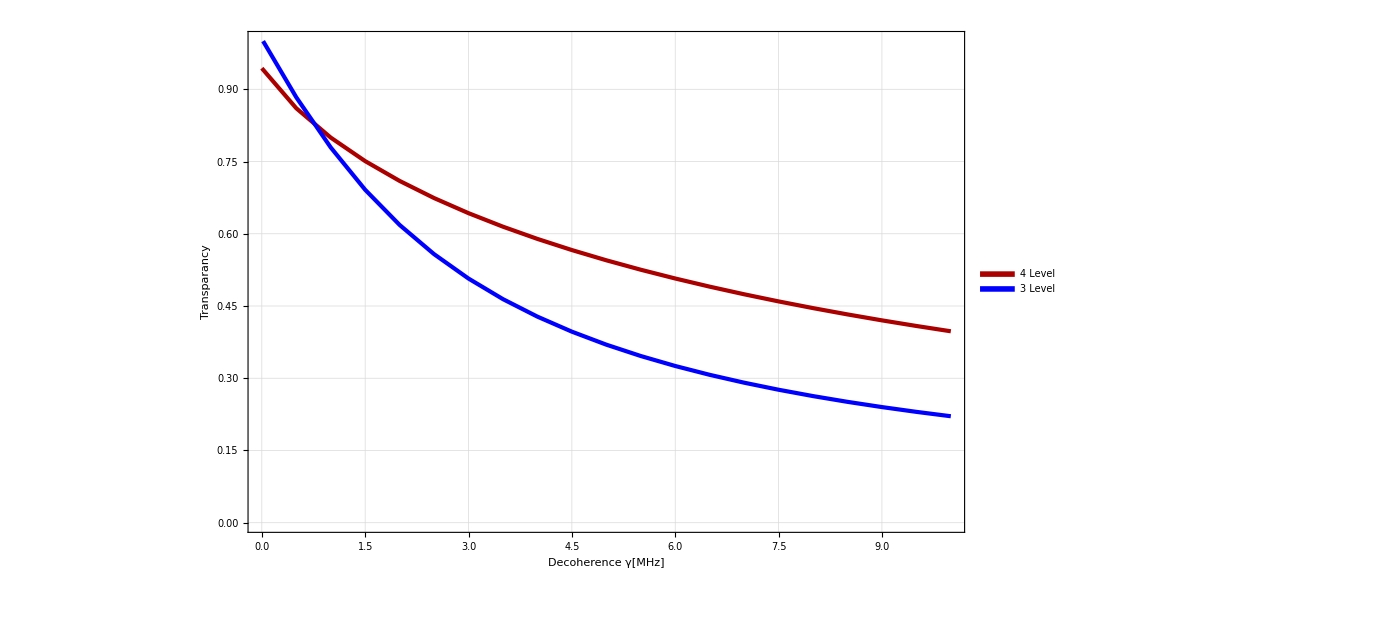

```mathematica
p=65;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

P=15γ

```mathematica
p=142.75;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

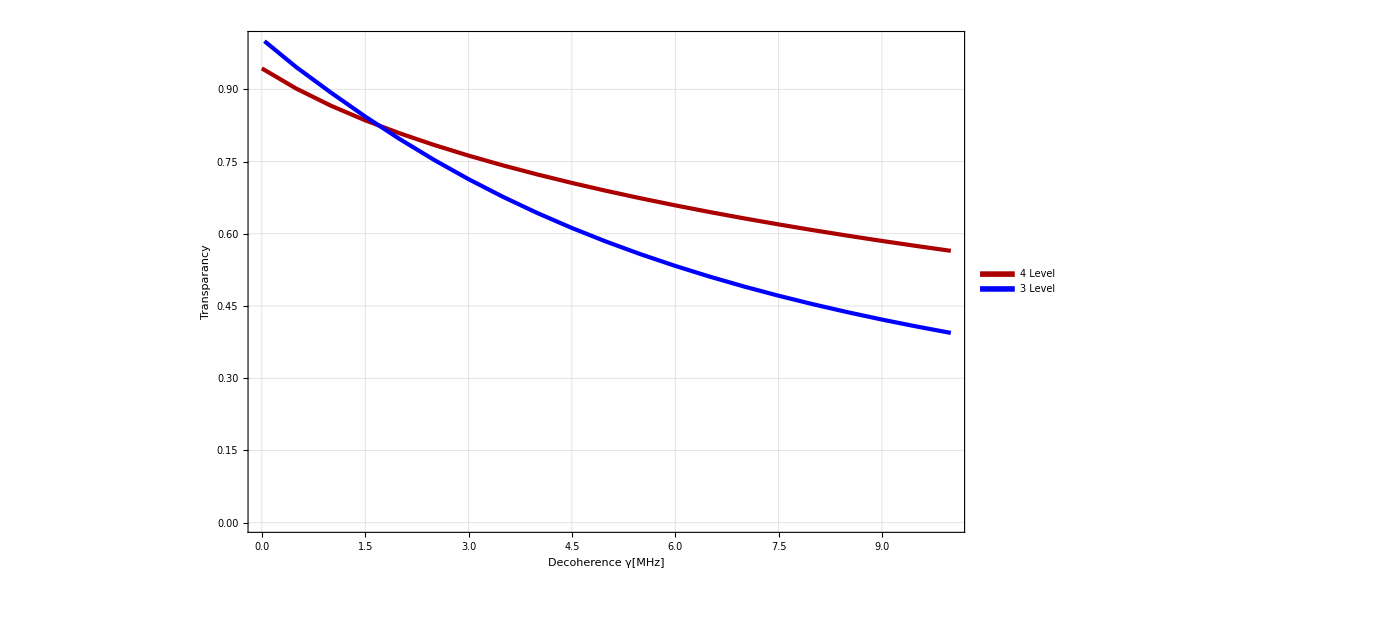

```mathematica
p=142.75;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

## FWHM vs power

γ=0

```mathematica
γ=0*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.002&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,3,200,25}]
]
```

Part::partw: Part 2 of {{{-0.00063,9.83952×10^-6},{-0.00062,9.74711×10^-6},{-0.00061,9.65333×10^-6},{-0.0006,9.55816×10^-6},{-0.00059,9.46162×10^-6},{-0.00058,9.36372×10^-6},{-0.00057,9.26447×10^-6},{0.00029,9.66721×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00063,9.83952×10^-6},{-0.00062,9.74711×10^-6},{-0.00061,9.65333×10^-6},{-0.0006,9.55816×10^-6},{-0.00059,9.46162×10^-6},{-0.00058,9.36372×10^-6},{-0.00057,9.26447×10^-6},{0.00029,9.66721×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.00016,9.13636×10^-6},{0.00014,8.9964×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00016,9.13636×10^-6},{0.00014,8.9964×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

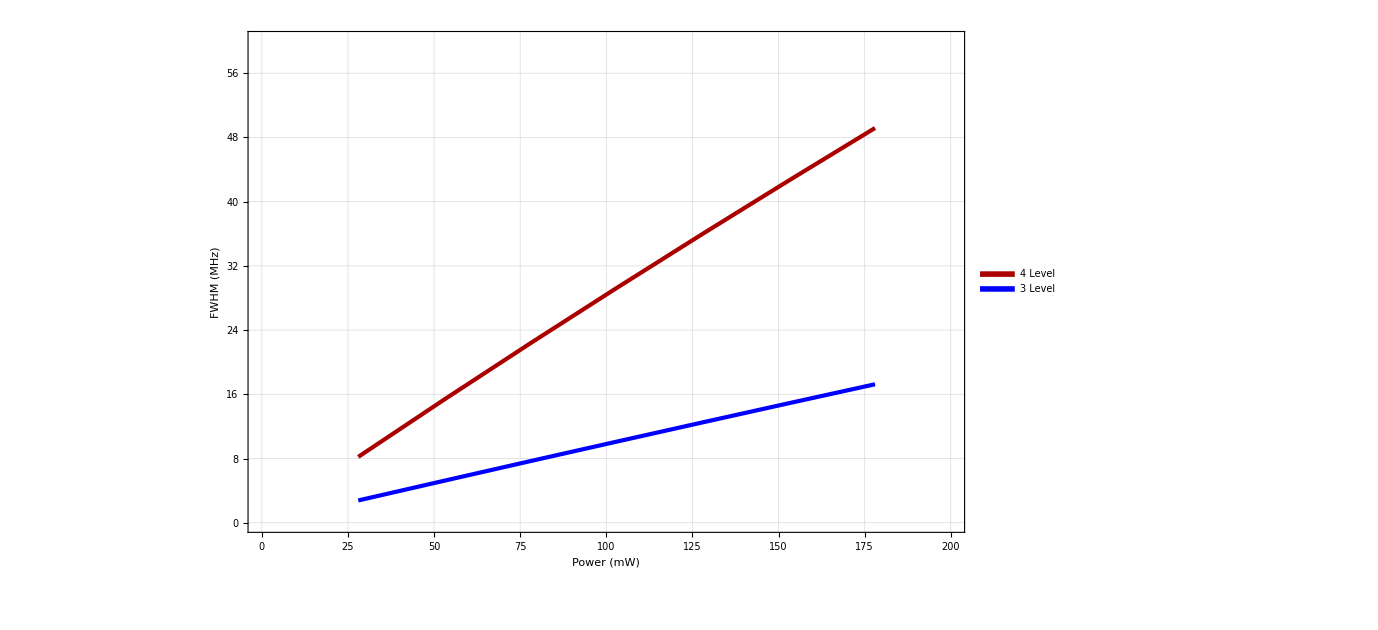

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

γ=0.1

```mathematica
γ=0.1*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,3,200,15}]
]
```

Part::partw: Part 2 of {{{-0.00197,0.0000150675},{-0.00196,0.0000150538},{-0.00195,0.00001504},{-0.00194,0.000015026},{-0.00193,0.000015012},{-0.00192,0.0000149979},{-0.00191,0.0000149836},{-0.0019,0.0000149693},{-0.00189,0.0000149548},{-0.00188,0.0000149403},{-0.00187,0.0000149256},{-0.00186,0.0000149109},{-0.00185,0.000014896},{-0.00184,0.000014881},{-0.00183,0.000014866},{-0.00182,0.0000148508},{-0.00181,0.0000148355},{0.00039,0.0000148753},{0.0004,0.0000149572},{0.00041,0.0000150391}}} does not exist.

Part::partd: Part specification {{{-0.00197,0.0000150675},{-0.00196,0.0000150538},{-0.00195,0.00001504},{-0.00194,0.000015026},{-0.00193,0.000015012},{-0.00192,0.0000149979},{-0.00191,0.0000149836},{-0.0019,0.0000149693},{-0.00189,0.0000149548},{-0.00188,0.0000149403},{-0.00187,0.0000149256},{-0.00186,0.0000149109},{-0.00185,0.000014896},{-0.00184,0.000014881},{-0.00183,0.000014866},{-0.00182,0.0000148508},{-0.00181,0.0000148355},{0.00039,0.0000148753},{0.0004,0.0000149572},{0.00041,0.0000150391}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.0017,0.0000165016},{-0.00169,0.0000164936},{-0.00168,0.0000164856},{-0.00167,0.0000164775},{-0.00166,0.0000164693},{-0.00165,0.0000164611},{-0.00164,0.0000164528},{-0.00163,0.0000164444},{-0.00162,0.000016436},{-0.00161,0.0000164275},{-0.0016,0.0000164189},{-0.00159,0.0000164103},{-0.00158,0.0000164016},{-0.00157,0.0000163928},{-0.00156,0.000016384},{-0.00155,0.0000163751},{0.00023,0.0000163781},{0.00024,0.0000164384},{0.00025,0.0000164988}}} does not exist.

Part::partd: Part specification {{{-0.0017,0.0000165016},{-0.00169,0.0000164936},{-0.00168,0.0000164856},{-0.00167,0.0000164775},{-0.00166,0.0000164693},{-0.00165,0.0000164611},{-0.00164,0.0000164528},{-0.00163,0.0000164444},{-0.00162,0.000016436},{-0.00161,0.0000164275},{-0.0016,0.0000164189},{-0.00159,0.0000164103},{-0.00158,0.0000164016},{-0.00157,0.0000163928},{-0.00156,0.000016384},{-0.00155,0.0000163751},{0.00023,0.0000163781},{0.00024,0.0000164384},{0.00025,0.0000164988}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

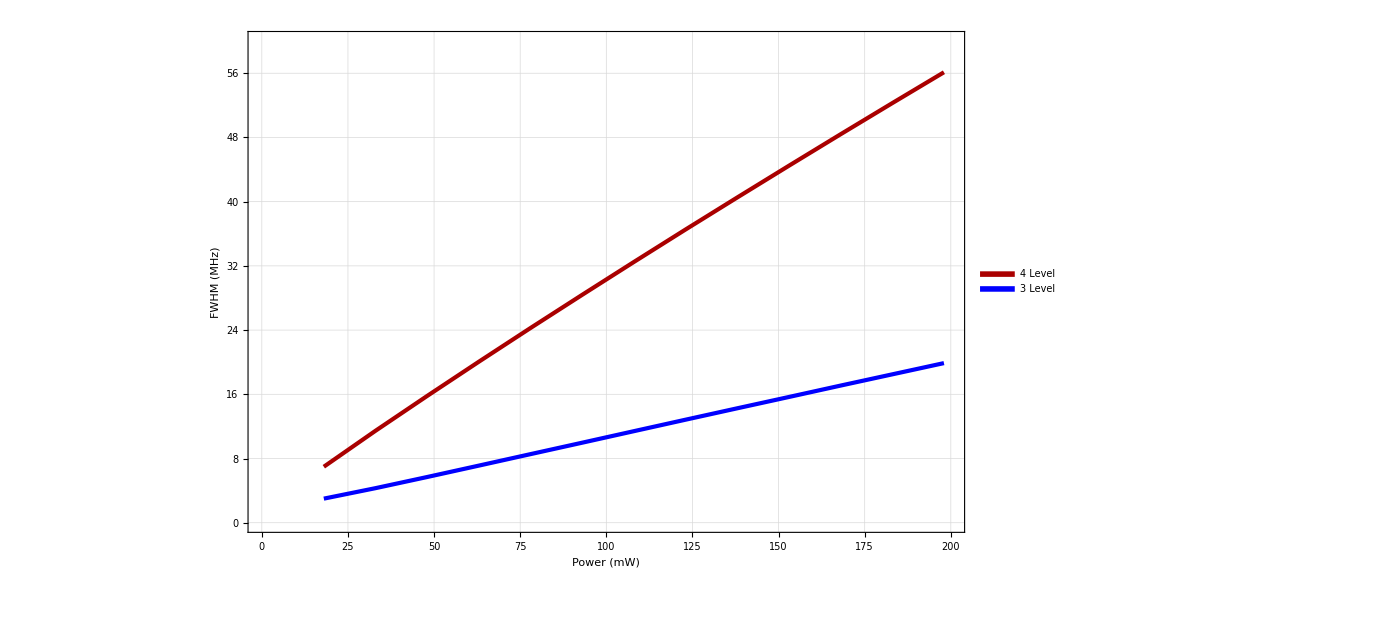

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

γ=0.25

80

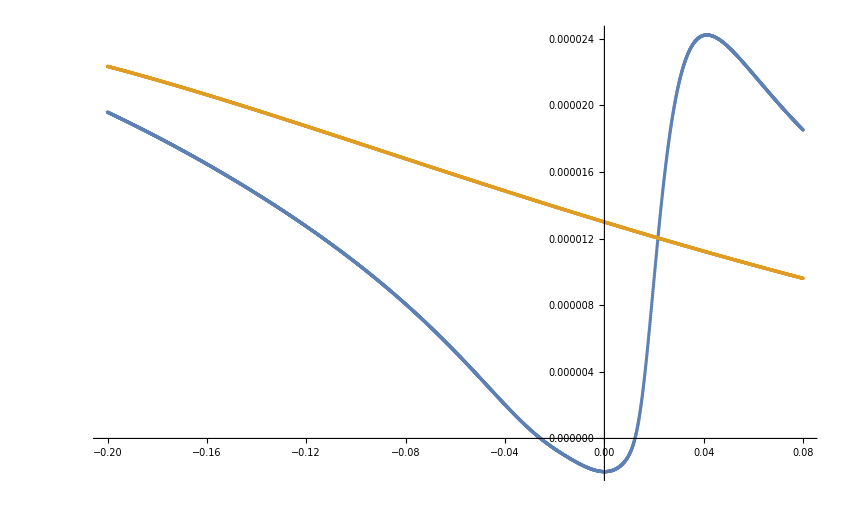

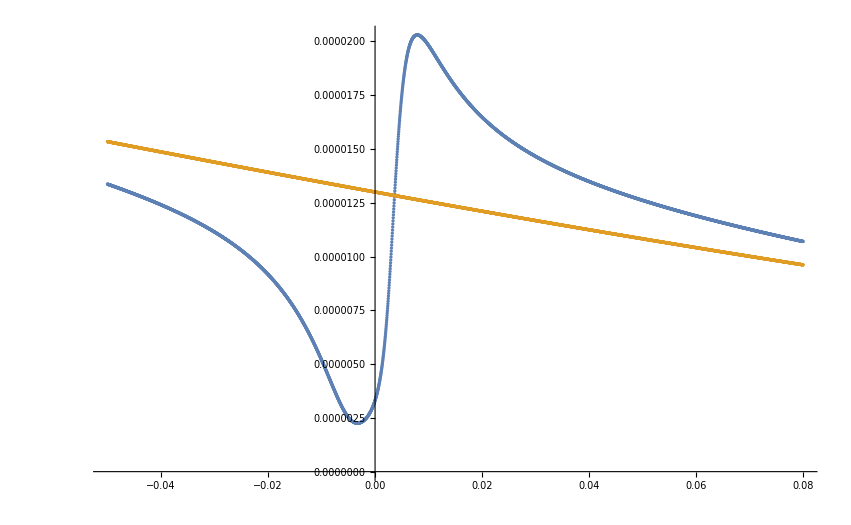

```mathematica
γ=0.25*5.750056;
p=80
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list,list1},PlotRange->All]
ListPlot[{list3,list4},PlotRange->All]
```

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 80/1000,
Select[Range[-0.20,0.05,0.000083],#≥ 0.0015∨#≤ -0.0015&]*10^9,
Range[-0.20,0.08,0.000083]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
γ=0.25*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
If[p<10,
list=Select[Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.015&];
list1=Select[Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.015&];
list3=Select[Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.005&];
list4=Select[Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.005&];,
list=Select[Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.05&];
list1=Select[Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.05&];
list3=Select[Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.02&];
list4=Select[Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.02&];
];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0025&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[-1]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0025&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[-1]][[All,1]]]]}];
,{p,3,200,2}]
]
```

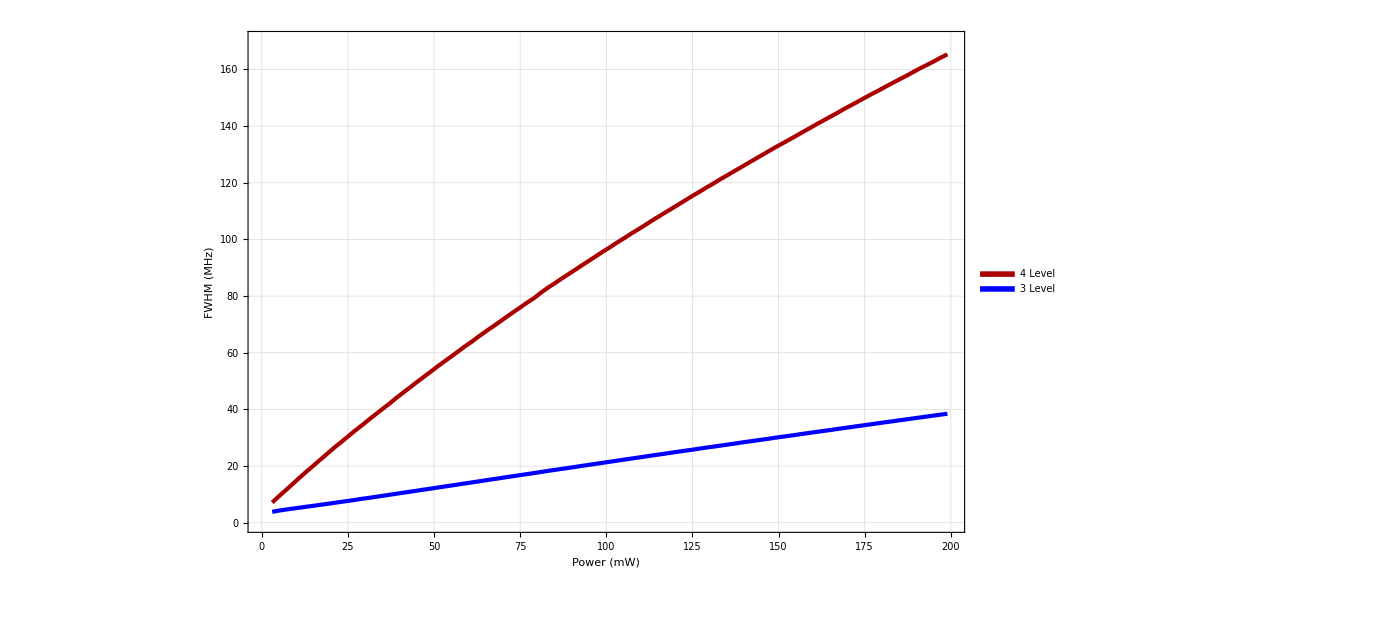

```mathematica
Fp1=ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,170}}]
```

```mathematica
Hey[list_]:=Transpose[{(Ome[list[[All,1]]/1000,1/1000]/(2 π 5.750056 10^6))^2,list⟦All,2⟧}]
```

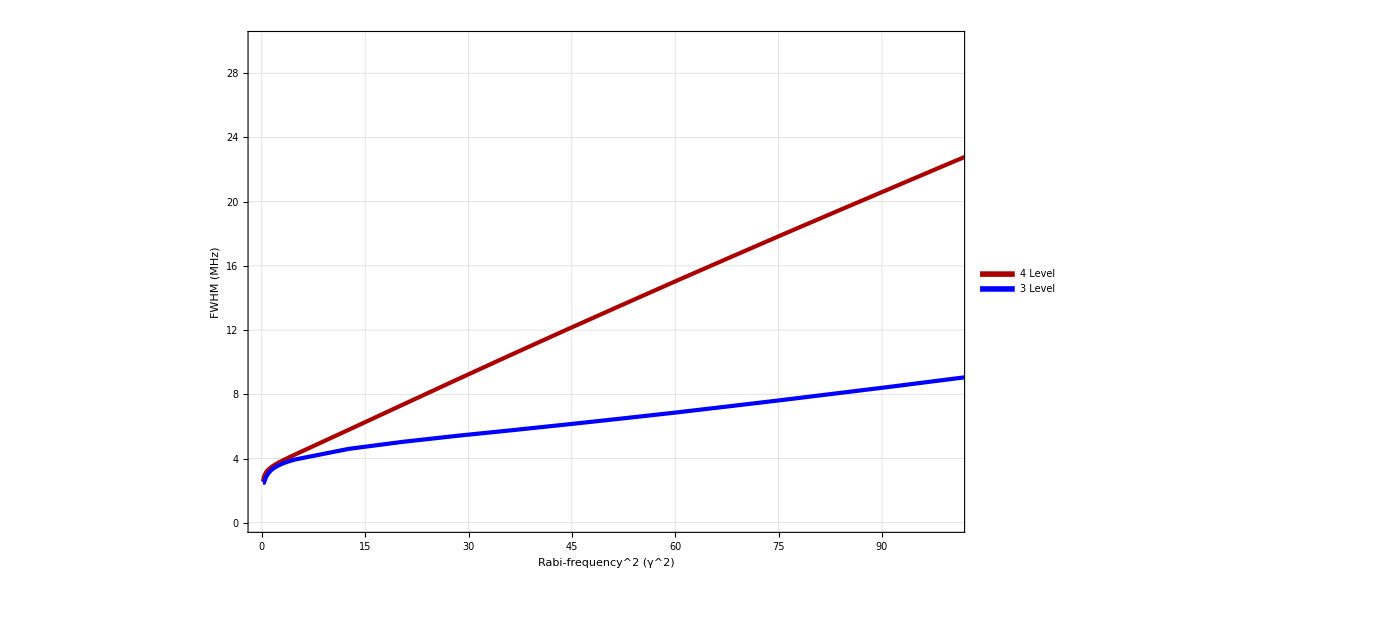

```mathematica
Fp1=ListPlot[{Hey[FvP4[γ]],Hey[FvP3[γ]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Rabi-frequency^2 Ω(γ^2)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,100},{0,30}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure43.eps",Fp1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure43.eps

γ=1

```mathematica
γ=1*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc3[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc3[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc3[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc3[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0015&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0015&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,1.5,25,2}]
]

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,25,200,25}]
]
```

Part::partw: Part 2 of {{{-0.00318,0.0000129368},{-0.00317,0.0000129364},{-0.00316,0.0000129361},{-0.00315,0.0000129357},{-0.00314,0.0000129354},{-0.00313,0.0000129351},{-0.00312,0.0000129347},{-0.00311,0.0000129344},{-0.0031,0.0000129341}}} does not exist.

Part::partd: Part specification {{{-0.00318,0.0000129368},{-0.00317,0.0000129364},{-0.00316,0.0000129361},{-0.00315,0.0000129357},{-0.00314,0.0000129354},{-0.00313,0.0000129351},{-0.00312,0.0000129347},{-0.00311,0.0000129344},{-0.0031,0.0000129341}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

$Aborted

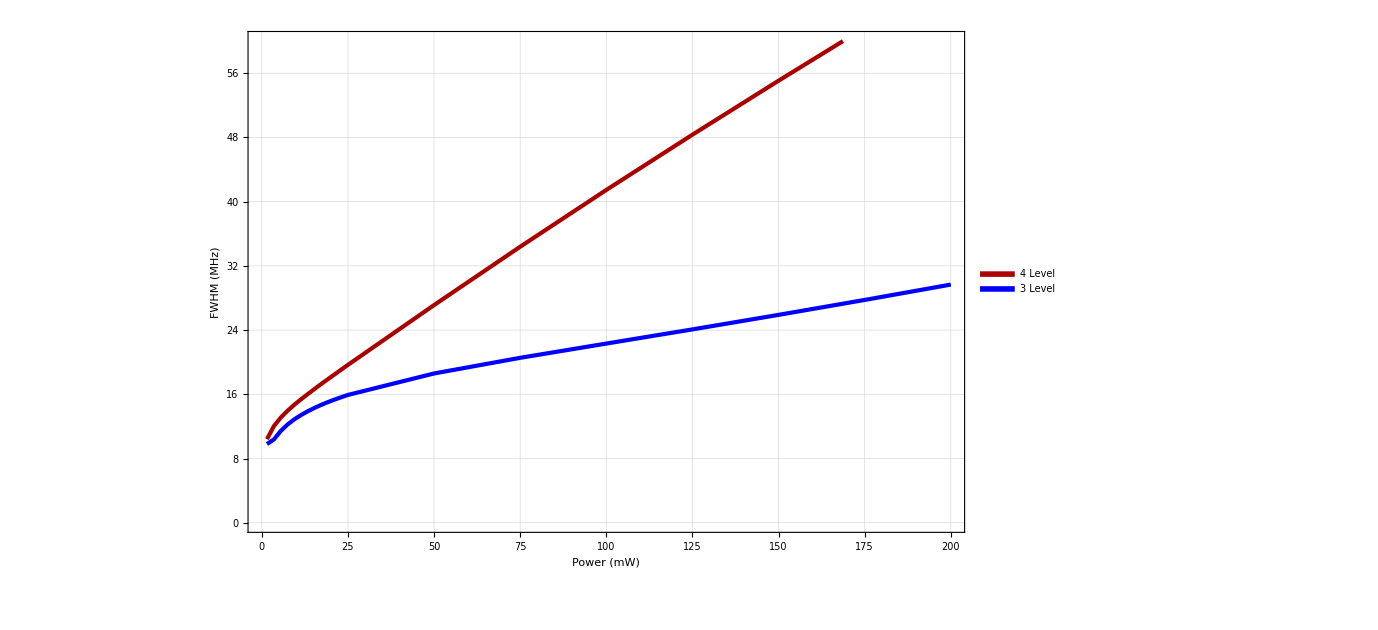

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

## FWHM vs dec

p=0

```mathematica
p=0;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.002&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.001&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

$Aborted

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,25}}]
```

-Graphics-

p=2.5

```mathematica
p=3.99;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc4[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc4[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc4[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc4[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0015&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0008&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

Part::partw: Part 2 of {{{-0.000844,9.88471×10^-6},{-0.000842,9.87098×10^-6},{-0.00084,9.85722×10^-6},{-0.000838,9.84343×10^-6},{-0.000836,9.82961×10^-6},{-0.000834,9.81576×10^-6},{-0.000832,9.80187×10^-6},{-0.00083,9.78796×10^-6},{-0.000828,9.77401×10^-6},{-0.000826,9.76004×10^-6},{-0.000824,9.74603×10^-6},«29»,{-0.000764,9.31132×10^-6},{-0.000762,9.29636×10^-6},{-0.00076,9.28136×10^-6},{-0.000758,9.26633×10^-6},{-0.000756,9.25128×10^-6},{-0.000754,9.23619×10^-6},{-0.000752,9.22107×10^-6},{0.00038,9.28893×10^-6},{0.000382,9.42374×10^-6},{0.000384,9.55804×10^-6},«2»}} does not exist.

Part::partd: Part specification {{{-0.000844,9.88471×10^-6},{-0.000842,9.87098×10^-6},{-0.00084,9.85722×10^-6},{-0.000838,9.84343×10^-6},{-0.000836,9.82961×10^-6},{-0.000834,9.81576×10^-6},{-0.000832,9.80187×10^-6},{-0.00083,9.78796×10^-6},{-0.000828,9.77401×10^-6},{-0.000826,9.76004×10^-6},{-0.000824,9.74603×10^-6},«29»,{-0.000764,9.31132×10^-6},{-0.000762,9.29636×10^-6},{-0.00076,9.28136×10^-6},{-0.000758,9.26633×10^-6},{-0.000756,9.25128×10^-6},{-0.000754,9.23619×10^-6},{-0.000752,9.22107×10^-6},{0.00038,9.28893×10^-6},{0.000382,9.42374×10^-6},{0.000384,9.55804×10^-6},«2»}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.00022,9.3729×10^-6},{-0.000218,9.30935×10^-6},{-0.000216,9.24449×10^-6},{-0.000214,9.17829×10^-6},{-0.000212,9.11071×10^-6},{-0.00021,9.04173×10^-6},{-0.000208,8.9713×10^-6},{-0.000206,8.8994×10^-6},{-0.000204,8.82599×10^-6},{-0.000202,8.75103×10^-6},{0.000184,8.81761×10^-6},{0.000186,8.98162×10^-6},{0.000188,9.14726×10^-6},{0.00019,9.31451×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00022,9.3729×10^-6},{-0.000218,9.30935×10^-6},{-0.000216,9.24449×10^-6},{-0.000214,9.17829×10^-6},{-0.000212,9.11071×10^-6},{-0.00021,9.04173×10^-6},{-0.000208,8.9713×10^-6},{-0.000206,8.8994×10^-6},{-0.000204,8.82599×10^-6},{-0.000202,8.75103×10^-6},{0.000184,8.81761×10^-6},{0.000186,8.98162×10^-6},{0.000188,9.14726×10^-6},{0.00019,9.31451×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.010246,0.00001802},{-0.010244,0.0000180199},{-0.010242,0.0000180198},{-0.01024,0.0000180198},{-0.010238,0.0000180197},{-0.010236,0.0000180197},{-0.010234,0.0000180196},{-0.010232,0.0000180195},{-0.01023,0.0000180195},{-0.010228,0.0000180194},{-0.010226,0.0000180194},{-0.010224,0.0000180193},«27»,{-0.010168,0.0000180176},{-0.010166,0.0000180176},{-0.010164,0.0000180175},{-0.010162,0.0000180174},{-0.01016,0.0000180174},{-0.010158,0.0000180173},{-0.010156,0.0000180172},{-0.010154,0.0000180172},{-0.010152,0.0000180171},{-0.01015,0.0000180171},{-0.010148,0.000018017},«141»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {{{-0.010246,0.00001802},{-0.010244,0.0000180199},{-0.010242,0.0000180198},{-0.01024,0.0000180198},{-0.010238,0.0000180197},{-0.010236,0.0000180197},{-0.010234,0.0000180196},{-0.010232,0.0000180195},{-0.01023,0.0000180195},{-0.010228,0.0000180194},{-0.010226,0.0000180194},{-0.010224,0.0000180193},«27»,{-0.010168,0.0000180176},{-0.010166,0.0000180176},{-0.010164,0.0000180175},{-0.010162,0.0000180174},{-0.01016,0.0000180174},{-0.010158,0.0000180173},{-0.010156,0.0000180172},{-0.010154,0.0000180172},{-0.010152,0.0000180171},{-0.01015,0.0000180171},{-0.010148,0.000018017},«141»}}⟦2⟧⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

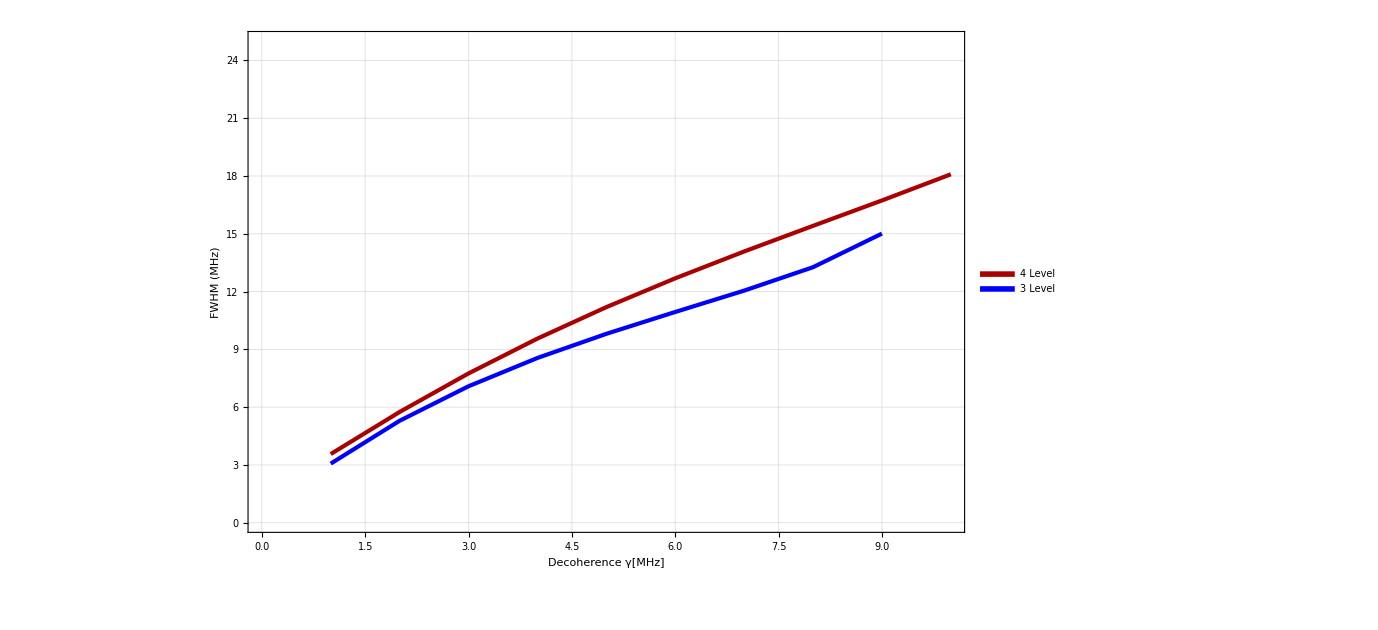

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,25}}]
```

p=5

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Flatten[{Range[-0.15,-0.0005,0.0002],Range[0.0006,0.05,0.00001]}]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Flatten[{Range[-0.15,-0.0081,0.0002],Range[-0.008,0.05,0.00001]}]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

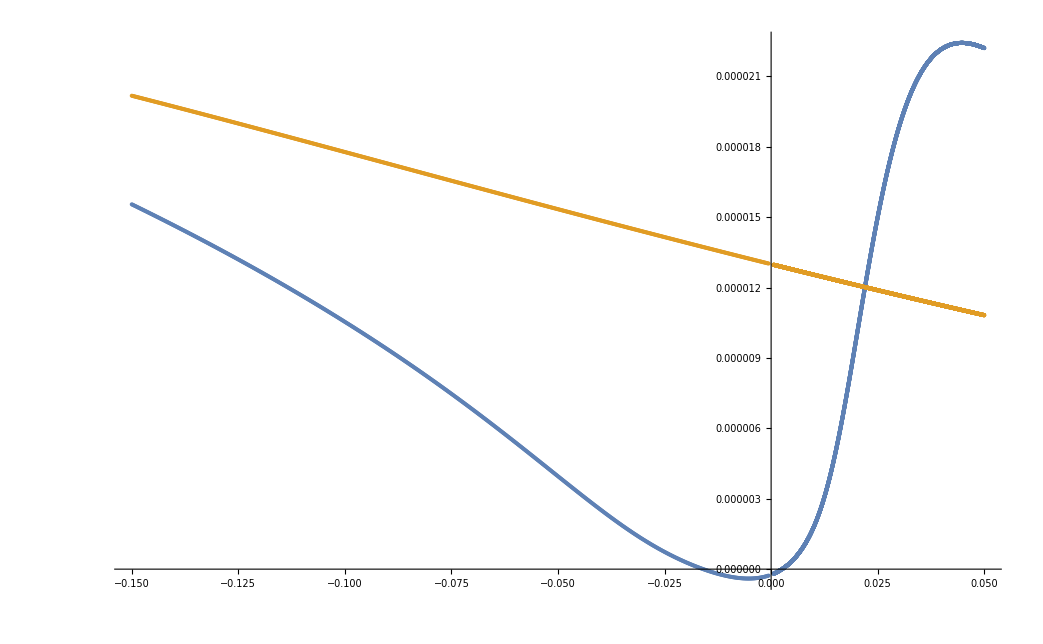

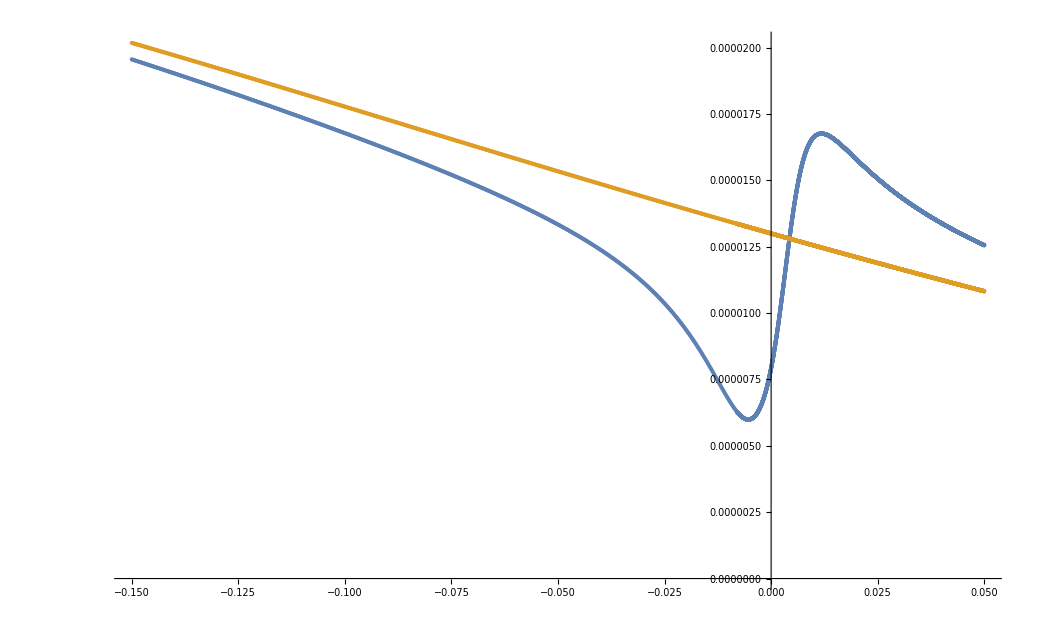

```mathematica
γ=5;
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list,list1},PlotRange->All]
ListPlot[{list3,list4},PlotRange->All]
```

```mathematica
p=15.8;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0025&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0025&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,5,.3}]
]
```

General::ovfl: Overflow occurred in computation.

```mathematica
nf1=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Fvγ4[p]
nf2=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Fvγ3[p]
```

{{0.,17.67},{0.0521734,18.52},{0.104347,19.255},{0.15652,19.89},{0.208694,20.52},{0.260867,21.155},{0.31304,21.785},{0.365214,22.425},{0.417387,22.965},{0.469561,23.505},{0.521734,24.055},{0.573907,24.6},{0.626081,25.055},{0.678254,25.61},{0.730428,26.065},{0.782601,26.53},{0.834774,27.095}}

{{0.,3.295},{0.0521734,3.76},{0.104347,4.33},{0.15652,4.955},{0.208694,5.605},{0.260867,6.25},{0.31304,6.88},{0.365214,7.495},{0.417387,8.02},{0.469561,8.635},{0.521734,9.24},{0.573907,9.65},{0.626081,10.16},{0.678254,10.68},{0.730428,11.095},{0.782601,11.52},{0.834774,11.855}}

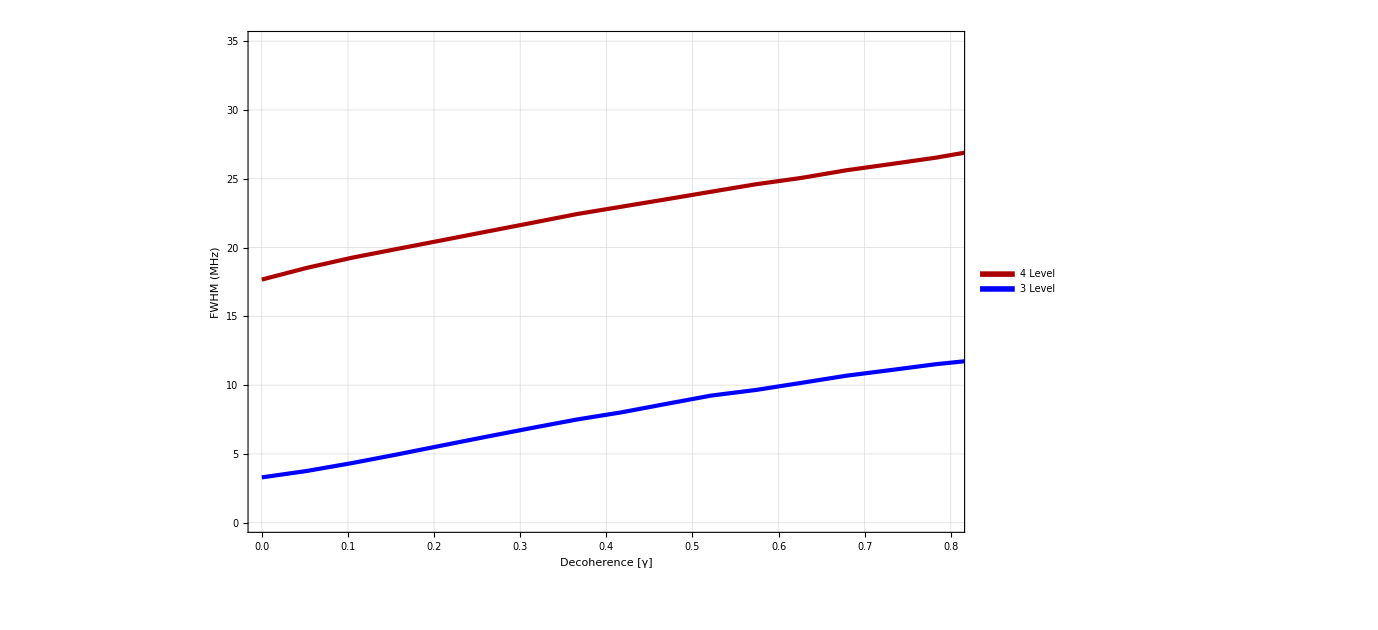

```mathematica
pd1=ListPlot[{nf1,nf2},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence [γ]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,0.8},{0,35}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure44.eps",pd1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure44.eps

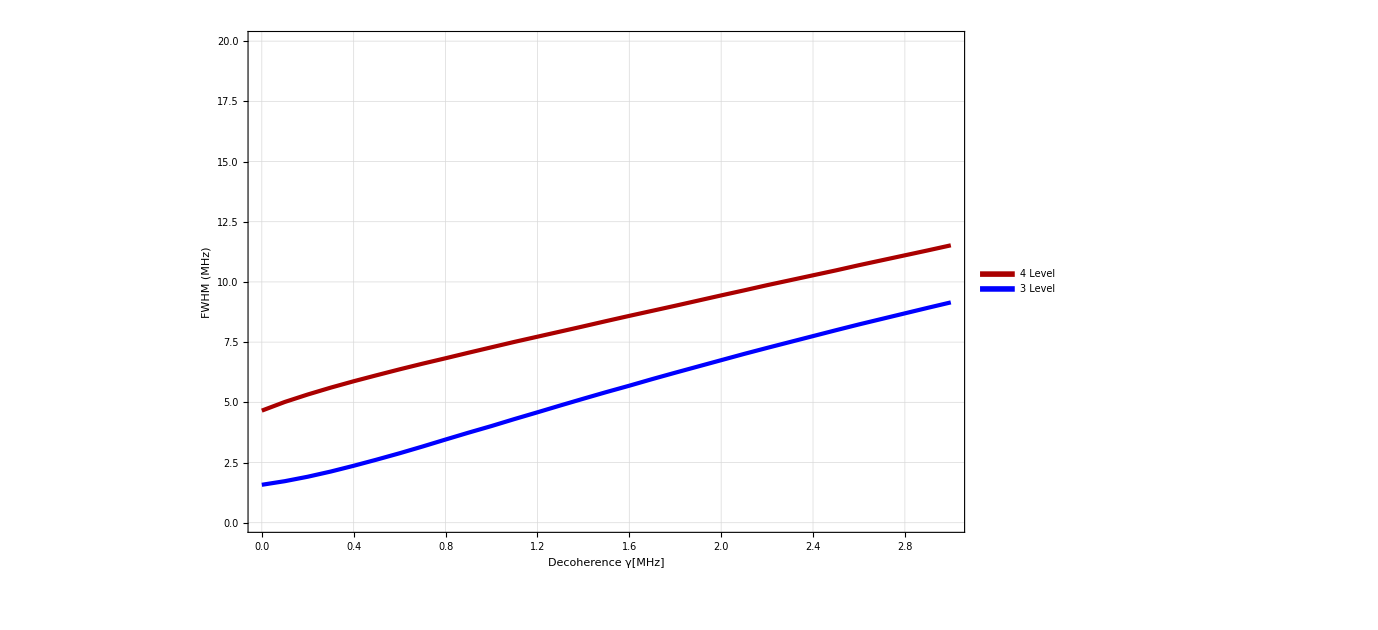

```mathematica
pd1=ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,3},{0,20}}]
```

p=10

```mathematica
p=65;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.005&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

```mathematica
.
```

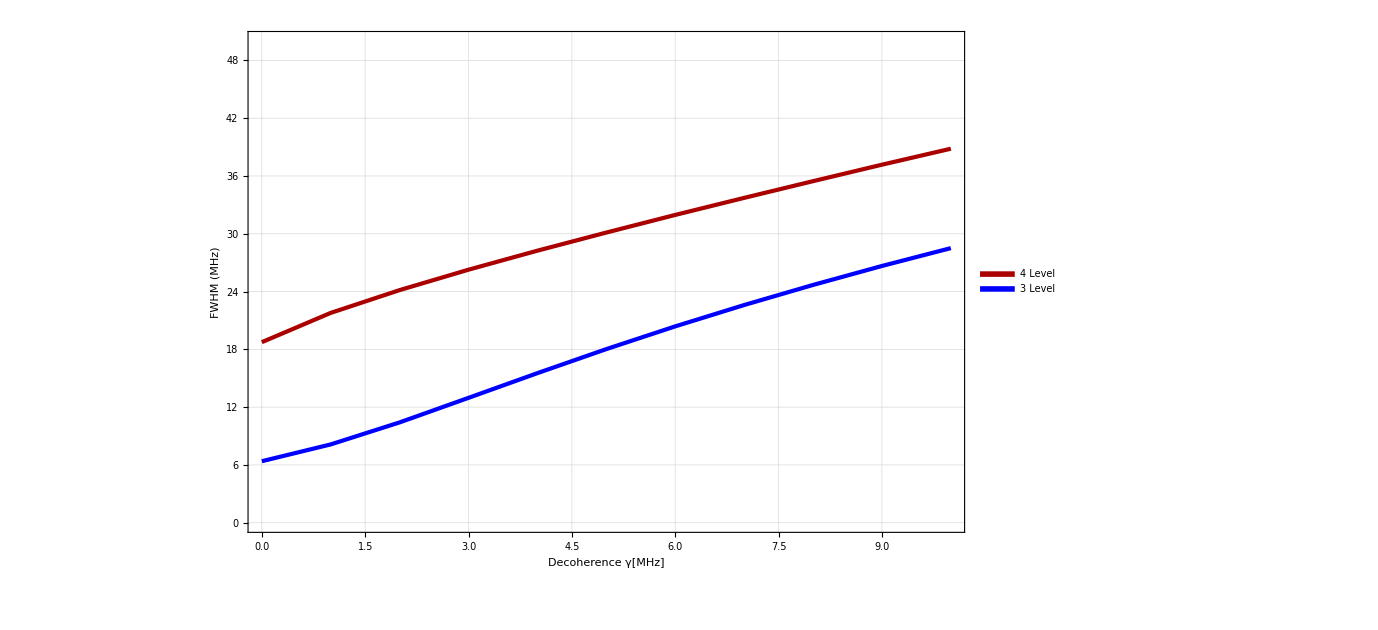

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,50}}]
```

p=15

```mathematica
p=145.75;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.005&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

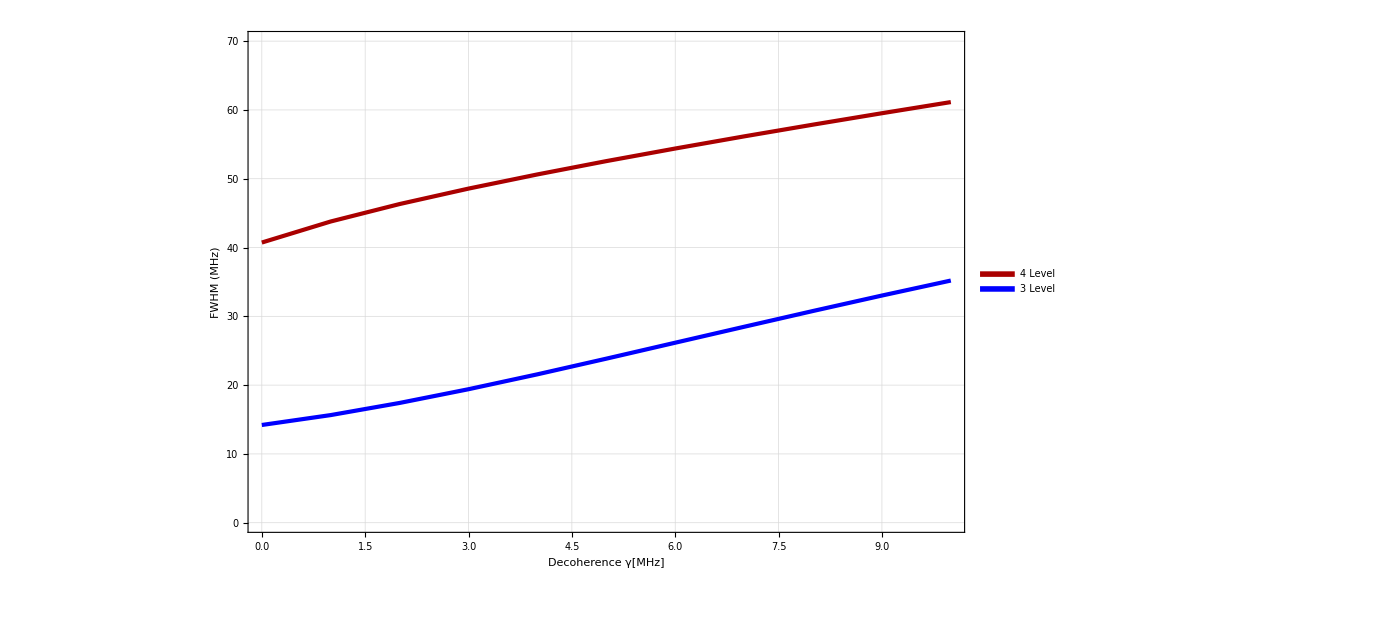

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,70}}]
```

# Save

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure4TvP.eps",tp1]
Export["Figure4TvD.eps",td1]
Export["Figure4FvP.eps",Fp1]
Export["Figure4Fvd.eps",pd1]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure4TvP.eps

Figure4TvD.eps

Figure4FvP.eps

Figure4Fvd.eps

```mathematica
pd1
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\2019-09-04 Final-Paper Figure"]
Export["Figure4TvD3.eps",td1]
Export["Figure4Fvd3.eps",pd1]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\2019-09-04 Final-Paper Figure

Figure4TvD3.eps

Figure4Fvd3.eps

```mathematica
tp1
```